# Introduction to Large Language Models and Retrieval Augmented Generation

## GDS Short Course - Day 2

March, 16, 2025

John McNally

Principal Academic Solutions Developer
Wolfram Research

## Syllabus

### Key questions

What is...

a large language model?

an embedding vector in latent space?

retrieval augmented generation?

a vector database?

### Key skills

In this segment, you will see how you can...

prompt large language models

create a semantic search index

create a simple AI agent

work with neural nets in Wolfram Language and Mathematica

## Language Models

A language model is simply a specific kind of artificial neural network. The most successful language models are currently based on a transformer architecture. It should be noted that transformers are not the only possible architecture and Mamba models for sequence learning are another notable option.

### Working with Neural Nets

OpenAI is releasing previews of GPT-4.5 these days, and you will see how to connect to this service later.

First, let’s first retrieve the open-source GPT-2 language model from the Wolfram Neural Net Repository:

```mathematica
languagemodel=NetModel["GPT2 Transformer Trained on WebText Data","Task"->"LanguageModeling"]
```

NetChain[<5>]

What does this neural net output?

```mathematica
languagemodel["hello world"]
```

.

Given some text, often called a prompt, the language model predicts the next bit of text.

Each bit of text in the vocabulary is called a token.

It turns out that the inability of early language models to do mathematics had a lot to do with suboptimal choices for how to tokenize text. This part of the course won’t go into details, but know that this step is actually non-trivial and has also come a long way since GPT-2:

```mathematica
languagemodel["2 + 2 ="]
```

3

Let’s look at the probability for multiple continuations:

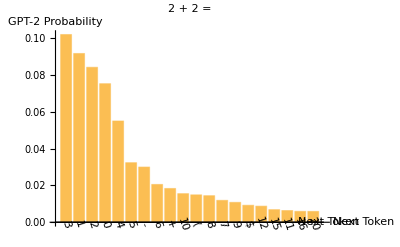

```mathematica
Module[{prompt,data},
prompt="2 + 2 =";data=ReverseSort@Association@languagemodel[prompt,{"TopProbabilities",20}];
BarChart[data,ChartLabels->Map[Rotate[#,-Pi/2.5]&,Keys@data],PlotLabel->Framed@Style[prompt,Bold],ImageSize->400,AxesLabel->{"Next Token","GPT-2 Probability"}]
]
```

Prompt engineering is the task of crafting prompts that nudge probabilities in a favorable direction for the behavior you want to see. Note that each generation of language models (and even each individual model) will have slightly different best practices for prompting.

Even this very old model nearly doubles its probability assignment for the desired response when told to play the role of an expert:

```mathematica
With[{
p1=languagemodel["You are an expert. Therefore, you know that 2 + 2 =",{"Probability"," 4"}],
p2=languagemodel["2 + 2 =",{"Probability"," 4"}]
},
p1/p2
]
```

1.84808

To speak very loosely, the additional context puts the language model in a very different “head space” for predicting next tokens:

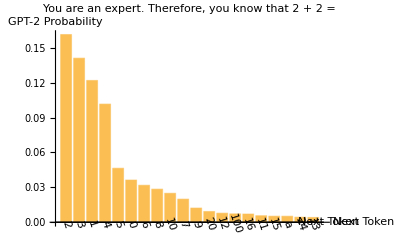

```mathematica
Module[{prompt,data},
prompt="You are an expert. Therefore, you know that 2 + 2 =";data=ReverseSort@Association@languagemodel[prompt,{"TopProbabilities",20}];
BarChart[data,ChartLabels->Map[Rotate[#,-Pi/2.5]&,Keys@data],PlotLabel->Framed@Style[prompt,Bold],ImageSize->400,AxesLabel->{"Next Token","GPT-2 Probability"},ImagePadding->{{Automatic,Automatic},{Automatic,25}}]
]
```

Let’s run a quick experiment to see how some text giving this model a role affects the probability assigned to the desired token. The results are amusing:

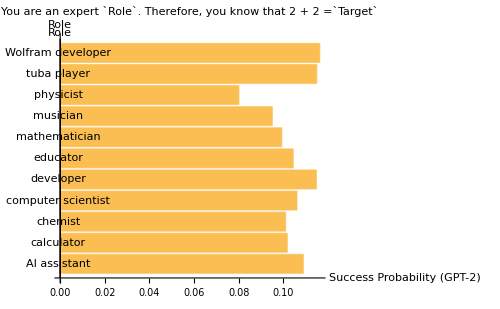

```mathematica
Module[{template,target,roles,prompts},
template=StringTemplate["You are an expert ``. Therefore, you know that 2 + 2 ="];
target=" 4";
roles=Sort@{"physicist","mathematician","educator","AI assistant","calculator","Wolfram developer","chemist","computer scientist","musician","tuba player","developer"};
prompts=Map[template,roles];
BarChart[languagemodel[prompts,{"Probability",target}],ChartLabels->roles,PlotLabel->Framed@Style[template["`Role`"]<>"`Target`",Bold],ImageSize->500,AxesLabel->{"Role","Success Probability (GPT-2)"},BarOrigin->Left,ImagePadding->{{Automatic,Automatic},{Automatic,15}}]
]
```

Keep in mind, this role-based prompt engineering is not always helpful as argued by Zheng et al (2024). However, this topic is still the subject of ongoing research such as Poterti et al (2025).

### Sampling and Temperature

In order to compute probabilities, the final layer of a language model will apply what is called a softmax layer by ML people. You might know this as a Boltzmann (Gibbs) distribution.

```mathematica
Information[languagemodel,"SummaryGraphic"]
```

-Graphics-

The outputs of the classification layer are the analog of the (negative) energies from statistical mechanics, and they are called logits in this context.

```mathematica
Manipulate[With[{data=ReverseSort@Association@manipulatenet[<|"Temperature"->Temperature,"String"->"2 + 2 ="|>,{"TopProbabilities",20}]},
BarChart[data,ChartLabels->Map[Rotate[#,-Pi/2.5]&,Keys@data],PlotRange->1,PlotLabel->Framed@Style["2 + 2 =",Bold],AspectRatio->1/2,AxesLabel->{"Next Token","Probability"}]
],{{Temperature,1},.05,2},TrackedSymbols:>Temperature,ControlPlacement->Top,Initialization:>With[{model=NetModel["GPT2 Transformer Trained on WebText Data","Task"->"LanguageModeling"]},manipulatenet=NetGraph[<|"logits"->NetTake[model,"classifier"],"scalar"->FunctionLayer[#logits/#t&],"probabilities"->SoftmaxLayer[]|>,{NetPort["String"]->NetPort["logits","Input"],"logits"->NetPort["scalar","logits"],
NetPort["Temperature"]->NetPort["scalar","t"],
"scalar"->"probabilities"},"String"->NetExtract[model,"Input"],"Output"->NetExtract[model,"Output"],"Temperature"->"Real"]]]
```

#### Your Turn

Look at the model’s structure to find the name of the layer preceding the SoftmaxLayer named “probabilities”:

```mathematica
languagemodel
```

NetChain[<5>]

Use NetTake to obtain the network up to that layer:

```mathematica
logitmodel=NetTake[languagemodel,"classifier"]
```

NetChain[<4>]

Use NetExtract to get the class labels for the tokenizer and decoder:

```mathematica
labels=NetExtract[NetExtract[languagemodel,NetPort["Output"]],"Labels"]
```

Compute the logits for possible continuations of “2 + 2 =”:

```mathematica
energies=-AssociationThread[labels->logitmodel["2 + 2 ="]]
```

Plot the result for the 10 “lowest energy” continuations:

```mathematica
With[{data=TakeSmallest[energies,10]},
ListPlot[KeyValueMap[{Callout[{-.25,#2},#1]}&,data],Axes->{False,True},GridLines->{None,Automatic},AxesLabel->{None,"- logits"},PlotMarkers->"▶"]
]
```

-Graphics-

### Transformer Architecture and Attention

You now know what a language model does, but how does one work?

The process is operationally a bit complicated but conceptually simple as seen in this summary graphic:

```mathematica
Information[languagemodel,"SummaryGraphic"]
```

-Graphics-

If you zoom in on the “embedding” block, notice that a raw token-level embedding is combined with a positional embedding. A transformer does not inherently take into account the order of input sequences, and so this positional embedding is needed for successfully learning language:

```mathematica
Information[NetExtract[languagemodel,"embedding"],"FullSummaryGraphic"]
```

-Graphics-

If you zoom in on the “decoder” block, there are multiple “attention blocks” inside. This is a graphic of one of them:

```mathematica
Information[NetExtract[languagemodel,{"decoder",1}],"FullSummaryGraphic"]
```

-Graphics-

Each attention block has multiple attention heads to “pay attention” to different parts of the data. The graphic below shows the weights for this four-token input:

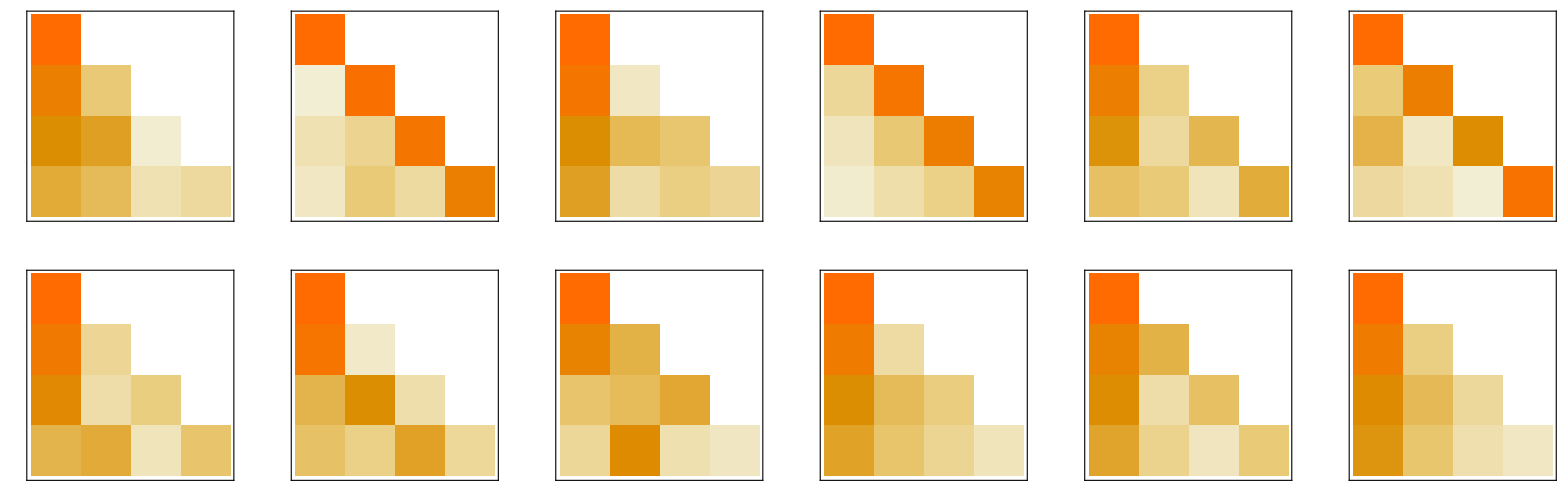
-Graphics-2 + 2 =

```mathematica
Module[{prompt,weights},
prompt="2 + 2 =";weights=NetModel["GPT2 Transformer Trained on WebText Data"][prompt,NetPort[{"decoder",1(*level*),1(*attention residual block*),"attention"(*attention block*),5(*attention layer*),"AttentionWeights"}]];
Labeled[GraphicsGrid[Partition[Table[MatrixPlot[weights[[All,n(*head*)]],
FrameTicks->None],{n,12}],6]],Framed@Style[prompt,"Text",Bold],Top]]
```

The above matrices being lower triangular are a consequence of using causal attention: the model can’t “cheat” by reading the end of a string before it is generated. Enforcing the causality constraint is relevant for text prediction but can have disadvantages for other applications.

## Vector Databases

A vector database is commonly used as a tool to give language models additional information that they wouldn’t know out-of-the-box. Vector databases allow search by semantic content, not just keywords.

### Embeddings of Text

In the graphical representation of GPT-2, notice that right before the classification layer, there is a 768-dimensional vector produced by the model:

```mathematica
Information[languagemodel,"SummaryGraphic"]
```

-Graphics-

In other words, the thing being classified to determine what should come next is an embedding vector in a latent space, not the text directly. This is a standard technique in language models and many kinds of classification tasks.

```mathematica
embeddingmodel=NetTake[languagemodel,"last"]
```

NetChain[<3>]

This model now maps strings to vectors. In the latent space, it is most common to use cosine distance as the relevant metric (as most embedding models also normalize their outputs).

You can compute the pairwise distance between embeddings in the latent space:

```mathematica
CosineDistance@@embeddingmodel[{"king","queen"}]
```

0.0272724

```mathematica
CosineDistance@@embeddingmodel[{"princess","queen"}]
```

0.00820108

You can get some sense of the topology of the embedding into the latent space space with plots like these:

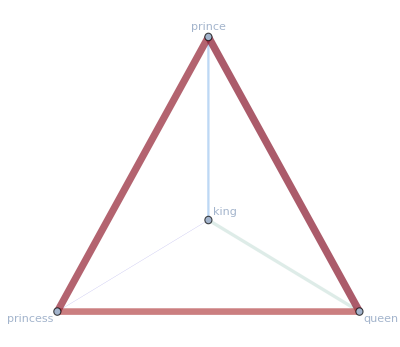

```mathematica
Module[{words,embeddings,graph,minmax},
words={"king","queen","prince","princess"};
embeddings=embeddingmodel@words;
graph=CompleteGraph[Length@words,VertexLabels->{v_:>words[[v]]},EdgeWeight->{i_<->j_:>CosineDistance[embeddings[[i]],embeddings[[j]]]}];
minmax=MinMax@AnnotationValue[graph,EdgeWeight];
Graph[graph,EdgeShapeFunction->Function[With[{w=AnnotationValue[{graph,#2},EdgeWeight]},{ColorData["ThermometerColors"][1-Rescale[w,minmax]],Thickness[(1-Rescale[w,minmax])/75],Line[#1]}]],EdgeLabels->Placed["EdgeWeight",Tooltip]]
]
```

One of the reasons why GPT-2 is less proficient than its newer cousins is because the embeddings it produces don’t map as cleanly onto our human intuitions of related concepts.

Compare to a different embedding model, BERT:

```mathematica
sentenceembedding=NetAppend[NetModel["BERT Trained on BookCorpus and Wikipedia Data"],"pooling"->SequenceLastLayer[]]
```

NetChain[<3>]

This embedding model maps a bit better onto human intuitions:

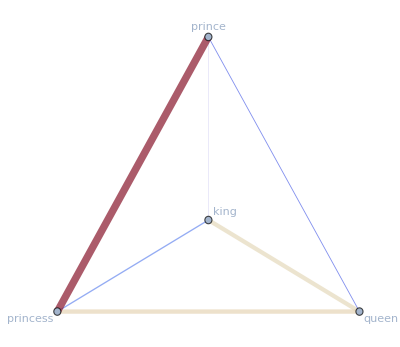

```mathematica
Module[{words,embeddings,graph,minmax},
words={"king","queen","prince","princess"};
embeddings=sentenceembedding@words;
graph=CompleteGraph[Length@words,VertexLabels->{v_:>words[[v]]},EdgeWeight->{i_<->j_:>CosineDistance[embeddings[[i]],embeddings[[j]]]}];
minmax=MinMax@AnnotationValue[graph,EdgeWeight];
Graph[graph,EdgeShapeFunction->Function[With[{w=AnnotationValue[{graph,#2},EdgeWeight]},{ColorData["ThermometerColors"][1-Rescale[w,minmax]],Thickness[(1-Rescale[w,minmax])/75],Line[#1]}]],EdgeLabels->Placed["EdgeWeight",Tooltip]]
]
```

A “better” embedding model, SentenceBERT, maps onto human intuition for analogies even more cleanly:

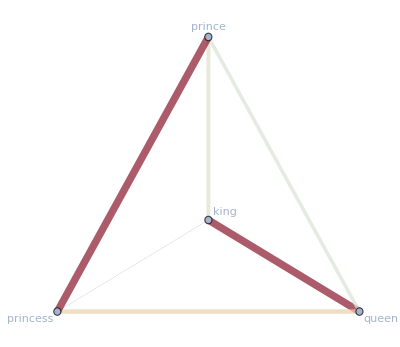

```mathematica
Module[{words,embeddings,graph,minmax},
words={"king","queen","prince","princess"};
embeddings=Normal@ResourceFunction["SentenceBERTEmbedding"]@words;
graph=CompleteGraph[Length@words,VertexLabels->{v_:>words[[v]]},EdgeWeight->{i_<->j_:>CosineDistance[embeddings[[i]],embeddings[[j]]]}];
minmax=MinMax@AnnotationValue[graph,EdgeWeight];
Graph[graph,EdgeShapeFunction->Function[With[{w=AnnotationValue[{graph,#2},EdgeWeight]},{ColorData["ThermometerColors"][1-Rescale[w,minmax]],Thickness[(1-Rescale[w,minmax])/75],Line[#1]}]],EdgeLabels->Placed["EdgeWeight",Tooltip]]
]
```

The (dimension-reduced) embeddings using this older model don’t give a particularly useful structure for analogy reasoning:

```mathematica
With[{words={{"king","queen"},{"prince","princess"}}},Labeled[Framed@{{"[◼]", "TextEmbeddingPlot"}}[words,2,Joined->True,PlotMarkers->Automatic,LabelingFunction->Callout,"EmbeddingFunction"->embeddingmodel,"ReductionMethod"->"MultidimensionalScaling"],Column[{Style["GPT-2 Embeddings","Text",Bold,GrayLevel[.4]],Style[StringRiffle[Map[StringRiffle[#," : "]&,words]," :: "],"Text",Bold,GrayLevel[.4]]},Alignment->Center],Top]
]
```

-Graphics-GPT-2 Embeddings
king : queen :: prince : princess

However, using a better embedding model (and appropriate dimension reduction) lets you “see” an analogy as mapped into the latent space:

```mathematica
With[{words={{"king","queen"},{"prince","princess"}}},Labeled[Framed@{{"[◼]", "TextEmbeddingPlot"}}[words,2,Joined->True,PlotMarkers->Automatic,LabelingFunction->Callout],Column[{Style["SentenceBERT Embeddings","Text",Bold,GrayLevel[.4]],Style[StringRiffle[Map[StringRiffle[#," : "]&,words]," :: "],"Text",Bold,GrayLevel[.4]]},Alignment->Center],Top]
]
```

-Graphics-SentenceBERT Embeddings
king : queen :: prince : princess

### Semantic Search

To use a vector database, the system will embed a query string, then return items whose embedding vectors are nearby the query vector.

Keep in mind this only works if the database strings and query string are embedded into a latent space using the same mapping (i.e., the same embedding model).

Here is an example search index of resource functions in our repository:

```mathematica
index=ResourceData["Semantic Index of Wolfram Function Repository Documentation"]
```

SemanticSearchIndex[…]

The following snippets of documentation are “close” to the user’s query in embedding space:

```mathematica
SemanticSearch[index,"I want to add semantic labels, such as units, to structured data.",{"Label","Item"},MaxItems->3]//Function[Dataset@Association@Thread[Range@Length@#->#]]
```

This is used extensively by our Notebook Assistant and variations on it.

## Retrieval Augmented Generation

The phenomenon of LLM hallucination occurs because language models will always say something, even if they don’t really have the appropriate context on which to generate appropriate text:

```mathematica
ChatEvaluate[ChatObject[],"What are all the topical groups of the American Physical Society? Please list them.",LLMEvaluator-><|"Model"->"gpt-4.5-preview"|>]
```

ChatObject[…]

Notice that the new model does helpfully link a web address to verify its claim. However, following that link reveals that the LLM response below is no longer up to date:

```mathematica
ResourceFunction["ImportMarkdownString"]@
```

As of October 2023, the American Physical Society (APS) lists the following topical groups:

1. Energy Research and Applications (GERA)
2. Few-Body Systems and Multiparticle Dynamics (GFB)
3. Gravitation (GGR)
4. Hadronic Physics (GHP)
5. Instrument and Measurement Science (GIMS)
6. Magnetism and its Applications (GMAG)
7. Medical Physics (GMED)
8. Physics Education Research (GPER)
9. Plasma Astrophysics (GPAP)
10. Precision Measurement & Fundamental Constants (GPMFC)
11. Quantum Information (GQI)
12. Shock Compression of Condensed Matter (GSCCM)
13. Soft Matter (GSOFT)
14. Statistical and Nonlinear Physics (GSNP)
15. Physics of Climate (GPC) 

These topical groups provide specialized forums for APS members to focus on areas of broad interest within physics, promoting collaboration, research dissemination, and dialogue within the physics community.

Note: APS continuously updates and modifies topical groups as appropriate. For the most accurate and up-to-date information, please visit the APS website directly: 
https://www.aps.org/membership/units/index.cfm

### Creating a Semantic Search Index

To automatically create a vector database associated with a source (in this case a wiki) you can use the CreateSemanticSearchIndex function:

```mathematica
index=CreateSemanticSearchIndex[
WikipediaData["American Physical Society"],
"APS Wiki Index",
Method-><|"SplitPattern"->StringExpression["\n\n\n"],"MinimumItemLength"->1,"MaximumItemLength"->1024|>
]
```

SemanticSearchIndex[…]

While you could create an LLMTool which the model would use, you can use an LLMPromptGenerator to programmatically add context:

```mathematica
generator=LLMPromptGenerator[index]
```

LLMPromptGenerator[…]

With a search of the index you have provided automatically conducted, the model will now answer according to the new information it was given:

```mathematica
ChatEvaluate[ChatObject[],"What are all the topical groups of the American Physical Society? Please list them.",LLMEvaluator-><|"Model"->"gpt-4.5-preview","Prompts"->generator|>]
```

ChatObject[…]

Note how the prompt and query that are used by default return the relevant information as the 5th context item in this case:

```mathematica
TabView@SemanticSearch[index,"What are all the topical groups of the American Physical Society? Please list them."]
```

12345678910

This is because the search index and query were generated in the simplest automated way. If you provide a better search query to the index, you get the desired result as the first item returned:

```mathematica
TabView@SemanticSearch[index,"topical groups"]
```

12345678910

Another best practice is to think more carefully about what you want to embed and then associate a payload to return for that query.

### Adding Annotations to a Semantic Search Index

With some string parsing, create an annotated list of sources and an annotated index:

```mathematica
annotatedindex=Module[{input,items,parts,annotated},
input=WikipediaData["American Physical Society"];
items=StringCases[input,"="..~~WhitespaceCharacter..~~Shortest[item__]~~WhitespaceCharacter..~~"="..:>item];
parts=StringSplit[input,"="..~~WhitespaceCharacter..~~Shortest[item__]~~WhitespaceCharacter..~~"="..];
annotated=Thread[items->MapThread[<|"Label"->#1,"Payload"->StringTrim@#2|>&,{items,Rest[parts]}]];
CreateSemanticSearchIndex[annotated,"Annotated APS",Method-><|"MinimumItemLength"->1|>]
]
```

SemanticSearchIndex[…]

Define a helper function to visualize the results:

```mathematica
semanticSearchVisualize[query_String]:=Module[{searchindex=annotatedindex,dbResult,data},
dbResult=Reverse@SemanticSearch[searchindex,query,{"Distance","Tags"}];
data=MapApply[Tooltip[10-#1,#2["Payload"]]&,Lookup[dbResult,{"Distance","Tags"}]];
BarChart[data,ChartLabels->Lookup[Lookup[dbResult,"Tags"],"Label"],BarOrigin->Left,AxesLabel->"Relevance Score",ImageSize->600]
]
```

Now, the most concise key phrase matches exceptionally well with the section heading that contains the desired info. The payload delivered to the model can be the text from that section:

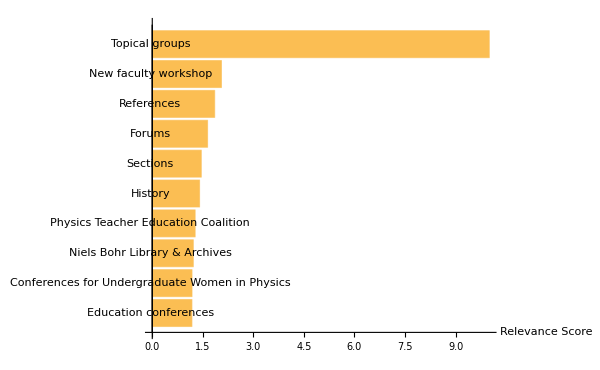

```mathematica
semanticSearchVisualize["topical groups"]
```

Using the user’s raw input still returns the desired section with highest relevance; however, the extraneous wording in the user’s raw input lowers the relevance score.

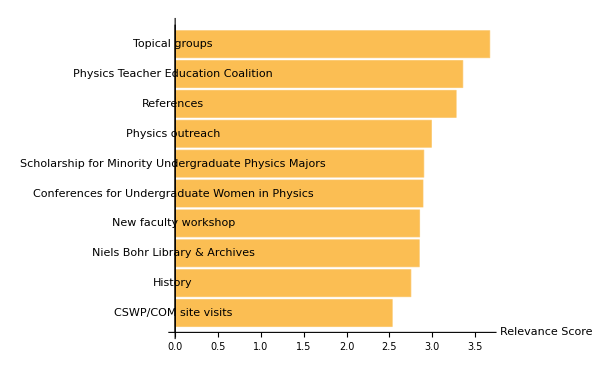

```mathematica
semanticSearchVisualize["What are all the topical groups of the American Physical Society? Please list them."]
```

To improve the search phrase used, you can use an LLM to summarize the user question into a search phrase:

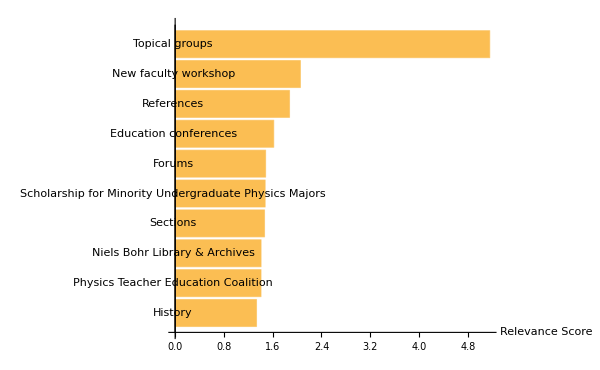
-Graphics-APS topical groups

```mathematica
With[{llmphrase=LLMSynthesize[{
"List ONE key search phrase to fulfill this request about the American Physical Society. Do not use quotation marks. Do not use \"American Physical Society\" in the phrase. Minimize the number of words used\n",
"What are all the topical groups of the American Physical Society? Please list them."
}]},
Labeled[semanticSearchVisualize[llmphrase],Style[llmphrase,"Text"],Top]
]
```

This can be combined into a more sophisticated generator of prompts:

```mathematica
bettergenerator=LLMPromptGenerator[];
```

You can hover over the tooltip to see what prompt was generated with this more sophisticated set-up:

```mathematica
ChatEvaluate[ChatObject[],"What are all the topical groups of the American Physical Society? Please list them.",LLMEvaluator-><|"Model"->"gpt-4.5-preview","Prompts"->bettergenerator|>]
```

prompt:  hover here

ChatObject[…]